# Quadratic NLS

### Two Modes

```mathematica
f[c0_,c1_]:=({{c0^2+2 c1^2}, {-1c1+2 c0 c1}})
h[θ1_]:=(-θ1)
```

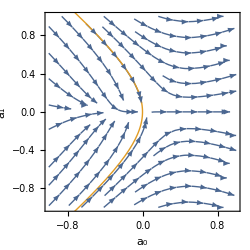
```mathematica
-Graphics--Graphics3D-
```

-Graphics- -Graphics3D-

### Three Modes

```mathematica
f[c0_,c1_,c2_]:=({{c0^2+2 c1^2+2 c2^2}, {-c1+2 c0 c1+2 c1 c2}, {-4c2 +2 c0 c2+c1^2}})
h[θ1_,θ2_]:=({{-θ1}, {-4 θ2+ 1/3 θ1^4}})
```

### Four Modes

```mathematica
f[c0_,c1_,c2_,c3_]:=({{c0^2+2 c1^2+2 c2^2+2 c3^2}, {-c1+2 c0 c1+2 c1 c2+2c3 c2}, {-4c2 +2 c0 c2+c1^2+2c3 c1}, {-9 c3 +2 c0 c3+2  c1 c2}})
h[θ1_,θ2_,θ3_]:=({{-θ1}, {-4 θ2+ 1/3 θ1^4}, {-9θ3-245/648 θ1^9-1/2 θ1 θ2^2}})
```

```mathematica
ω=2π;
F[a0_,a1_,a2_,a3_]:={ a0^2+2(a1^2+a2^2 +a3^2),-ω^2 1a1+ (2 a2 a1+  2 a3 a2) +  2 a0 a1,  -ω^2 2^2 a2+(a1 a1+ (2 a3 a1) )+  2 a0  a2,  -ω^2 3^2 a3 +(2 a1 a2 )+   2 a0 a3}
```

```mathematica
A0O=-5.3078;
A1O=15;
A2O=0;
A3O=0;

Tmax=3.6;
sol=NDSolve[{{a0'[t],a1'[t],a2'[t],a3'[t]}== I F[a0[t],a1[t],a2[t],a3[t]],
{a0[0],a1[0],a2[0],a3[0]}== {A0O,A1O,A2O,A3O}
},
{a0,a1,a2,a3},{t,0,Tmax},AccuracyGoal->15,PrecisionGoal->12];
```

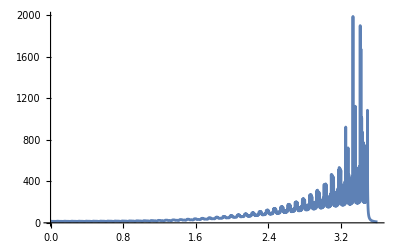

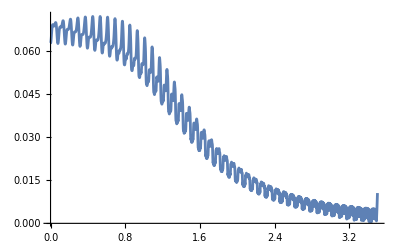

```mathematica
p=2;
Plot[Evaluate[{(Abs[a0[t]]^p+Abs[a1[t]]^p+Abs[a2[t]]^p+Abs[a3[t]]^p)^(1/p)}/.sol],{t,0,Tmax},PlotRange->All]
Plot[Evaluate[{1/(Abs[a0[t]]^p+Abs[a1[t]]^p+Abs[a2[t]]^p+Abs[a3[t]]^p)^(1/p)}/.sol],{t,0,3.5},PlotRange->All]
```

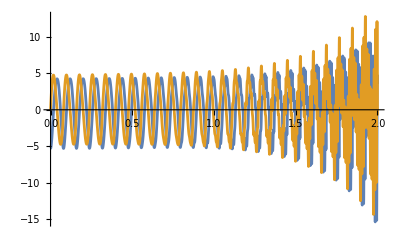

```mathematica
Plot[Evaluate[{Re[a0[t]],Im[a0[t]]}/.sol],{t,0,2},PlotRange->All]
```

```mathematica
g0=Plot[Evaluate[{Abs[a0[t]]}/.sol],{t,2 ,Tmax},PlotRange->All,AspectRatio->1];
g1=Plot[Evaluate[{,Abs[a1[t]]}/.sol],{t,2 ,Tmax},PlotRange->All,AspectRatio->1];g2=Plot[Evaluate[{,,Abs[a2[t]]}/.sol],{t,2 ,Tmax},PlotRange->All,AspectRatio->1];g3=Plot[Evaluate[{,,,Abs[a3[t]]}/.sol],{t,2 ,Tmax},PlotRange->All,AspectRatio->1];
```

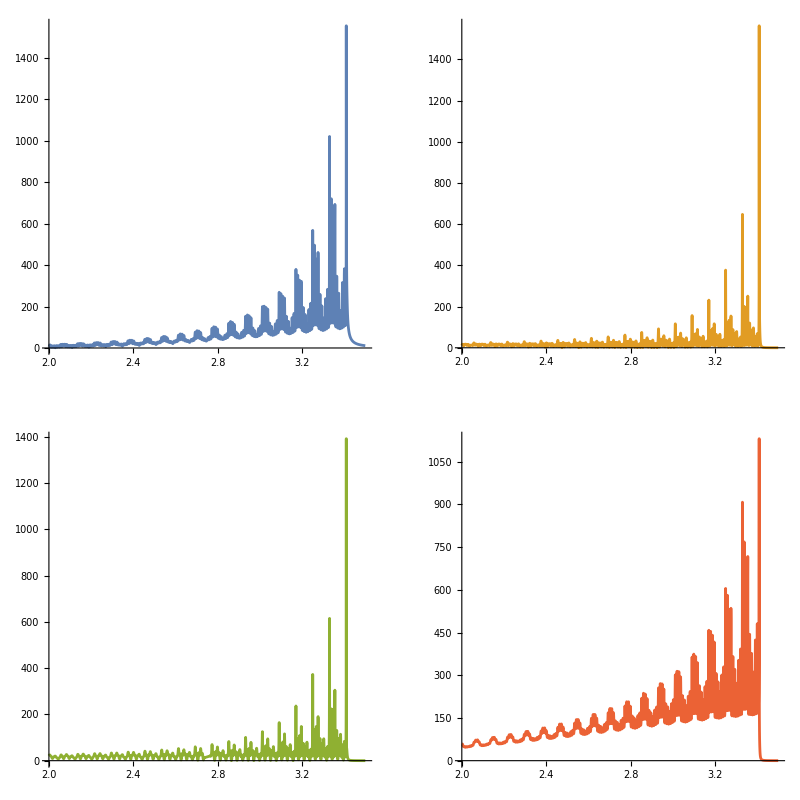

```mathematica
GraphicsGrid[{{g0,g1},{g2,g3}}]
```

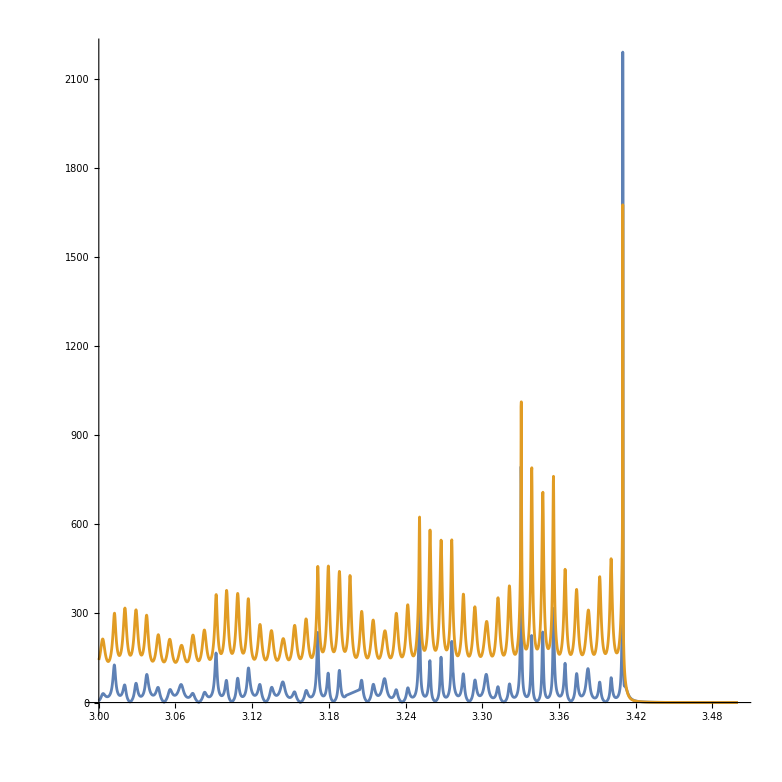

```mathematica
g3=Plot[Evaluate[{Abs[a2[t]],Abs[a3[t]]}/.sol],{t,3 ,Tmax},PlotRange->All,AspectRatio->1]
```

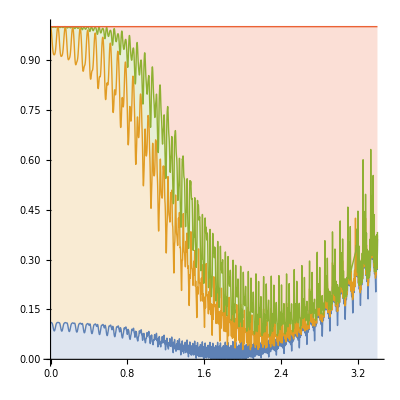

```mathematica
Plot[Evaluate[{Abs[a0[t]]^2/(Abs[a0[t]]^2+Abs[a1[t]]^2+Abs[a2[t]]^2+Abs[a3[t]]^2),(Abs[a0[t]]^2+Abs[a1[t]]^2)/(Abs[a0[t]]^2+Abs[a1[t]]^2+Abs[a2[t]]^2+Abs[a3[t]]^2),(Abs[a0[t]]^2+Abs[a1[t]]^2+Abs[a2[t]]^2)/(Abs[a0[t]]^2+Abs[a1[t]]^2+Abs[a2[t]]^2+Abs[a3[t]]^2),1}/.sol],{t,0 ,3.4},PlotRange->All,AspectRatio->1,Filling->{{1->Axis},{2->{1}},{3->{2}},{4->{3}}},PlotStyle->Thin]
```

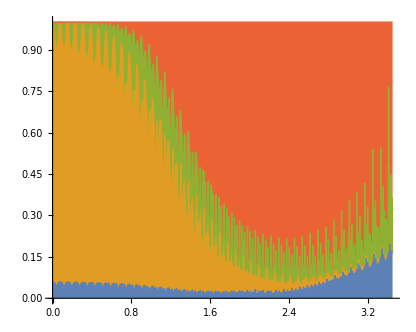

```mathematica
RelativeModes = Plot[Evaluate[{Abs[a0[t]]^2/(Abs[a0[t]]^2+2 Abs[a1[t]]^2+2 Abs[a2[t]]^2+2 Abs[a3[t]]^2),(Abs[a0[t]]^2+2 Abs[a1[t]]^2)/(Abs[a0[t]]^2+2 Abs[a1[t]]^2+2 Abs[a2[t]]^2+2 Abs[a3[t]]^2),(Abs[a0[t]]^2+2 Abs[a1[t]]^2+2 Abs[a2[t]]^2)/(Abs[a0[t]]^2+2 Abs[a1[t]]^2+2 Abs[a2[t]]^2+2 Abs[a3[t]]^2),1}/.sol],{t,0 ,3.45},PlotRange->All,AspectRatio->1/1.25,Filling->{{1->Axis},{2->{1}},{3->{2}},{4->{3}}},PlotStyle->Thin,FillingStyle->Directive[Opacity[1]]]
```

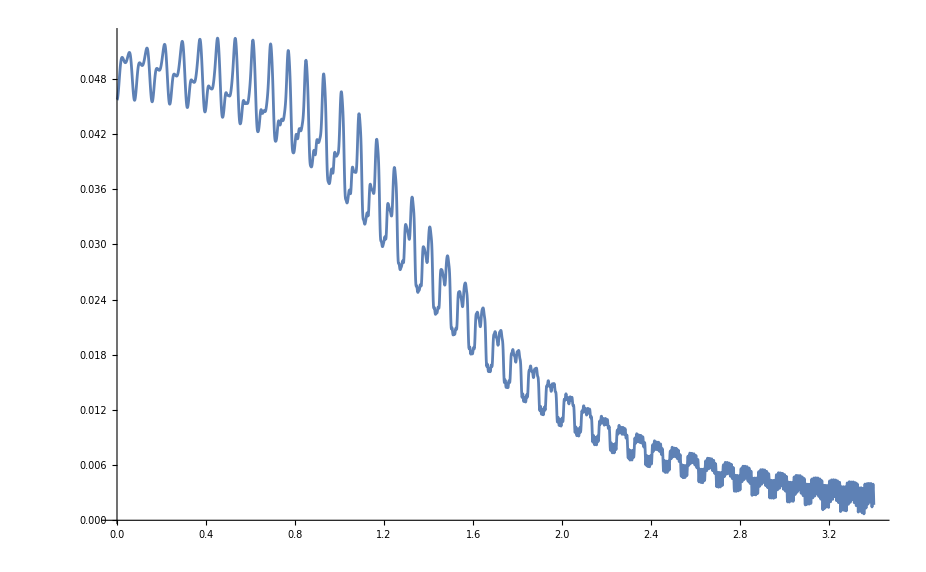

```mathematica
NormInverse = Plot[Evaluate[{√(1/(Abs[a0[t]]^2+2 Abs[a1[t]]^2+2 Abs[a2[t]]^2+2 Abs[a3[t]]^2))}/.sol],{t,0 ,3.4},PlotRange->All]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\JonoS\Dropbox\etc\NLS\Real_initial_data\Mathematica

```mathematica
Export["RelativeModes.png",RelativeModes]
```

RelativeModes.png

```mathematica
Shading
```

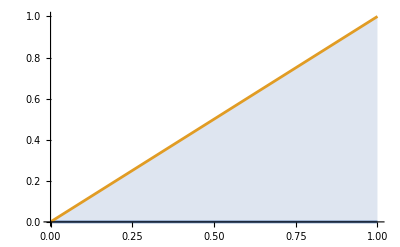

```mathematica
Plot[{0,x},{x,0,1},Filling->{1->{2}}]
```